```mathematica
f[μ_,x_]:= μ x(1-x)
```

```mathematica
graficoOrbita[μ_,x_,n_]:=Module[
{
pts=Table[{ξ,ξ},{ξ,NestList[f[μ,#]&,x,n]}]
},
Plot[{f[μ,t],t},{t,Min[x,0],Max[x,1]},PlotStyle->{{Black}},AspectRatio->Automatic,PlotRange->All,Epilog->{{Blue,Thin,Line[{First[#],{First[First@#],Last[Last@#]},Last[#]}]&/@Partition[pts,2,1]},{Red,Thick,Point/@Drop[pts,-1]},{Cyan,Thick,Point[pts//Last]}}]]
```

```mathematica
orbita[μ_,x_,n_]:=NestList[f[μ,#]&,x,n]
```

```mathematica
pattrattivi=Cases[Import[ToString[NotebookDirectory[]]<>"attr.csv","CSV"],{x_,y_}/;x>1  y>10^-3]
```

{{1.0012,0.00119857},{1.0012,0.00119857},{1.0012,0.00119857},{1.0012,0.00119857},{1.0012,0.00119857},{1.0012,0.00119857},{1.0012,0.00119857},{1.0012,0.00119857},{1.0012,0.00119857},{1.0012,0.00119857},39286,{4.,0.794207},{4.,0.817737},{4.,0.826142},{4.,0.86467},{4.,0.896727},{4.,0.903475},{4.,0.906357},{4.,0.93986},{4.,0.956103}}
 |  |  |  |

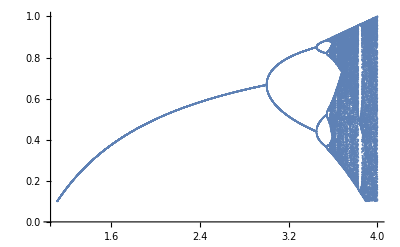

```mathematica
ListPlot[pattrattivi]
```

```mathematica
Join[Drop[pattrattivi,1],{0}]
```

```mathematica
Riffle[First/@pattrattivi,Differences[]]
```

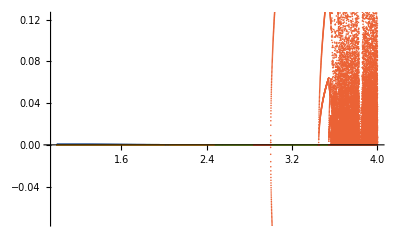

```mathematica
ListPlot[FindClusters[Partition[Riffle[First/@pattrattivi,Differences[Last/@pattrattivi]],2]]]
```

```mathematica
fn[μ_,x_,n_]:= Nest[f[μ,#]&,x,n]
```

```mathematica
dfn[μ_,x_,n_]:=D[fn[μ,x,n], x]-1
```

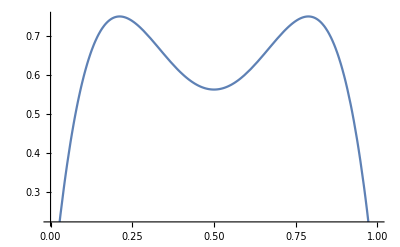

```mathematica
Plot[fn[3,x,2],{x,0,1}]
```

```mathematica
x[μ_,n_]:= FixedPoint[fn[μ,#,n]&,0.5,100]
```

0.643301

x=f^2(x), df^2 df^2(x)==x

$Aborted

```mathematica
g[μ_,n_]:= dfn[μ,ξ,n]/.{ξ->x[μ,n]}
```

```mathematica
g[μ,2]
```

-1+μ^2-2 μ^2 x[μ,2] (1+μ+μ x[μ,2] (-3+2 x[μ,2]))

```mathematica
Plot[g[μ,2],{μ,0,4}]
```

-Graphics-

```mathematica
g[μ_,n_]:=With[{x=NSolve[{z==fn[μ,z,n],0<z≤1},z,Reals][[1,1,2]]},D[fn[μ,ξ,n],ξ]/.{ξ:>x}]
```

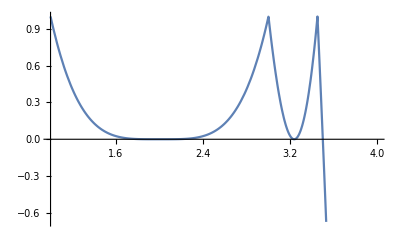

```mathematica
Plot[g[μ,4],{μ,1,4}]
```

```mathematica
NSolve[{z==fn[0.5,z,2],0<z≤1}]
```

NSolve[{z==f[0.5,f[0.5,z]],0<z≤1}]

```mathematica
NSolve[{z==fn[μ,z,n],0<z≤1},z,Reals]
```

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[f[μ,#1]&,z,n].

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[{z==Nest[f[μ,#1]&,z,n],0<z≤1},z,ℝ]

```mathematica
g[μ,4]
```

Part::partw: Part 1 of {} does not exist.

μ^4 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧) (1-μ^2 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧)) (-μ^3 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧) (-μ^2 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (-μ (1-{}⟦1,1,2⟧)+μ {}⟦1,1,2⟧)-μ^2 (1-{}⟦1,1,2⟧) (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧)+μ^2 {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧))-μ^3 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (-μ (1-{}⟦1,1,2⟧)+μ {}⟦1,1,2⟧) (1-μ^2 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧))-μ^3 (1-{}⟦1,1,2⟧) (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧) (1-μ^2 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧))+μ^3 {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧) (1-μ^2 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧)))+μ^4 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧) (-μ^2 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (-μ (1-{}⟦1,1,2⟧)+μ {}⟦1,1,2⟧)-μ^2 (1-{}⟦1,1,2⟧) (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧)+μ^2 {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧)) (1-μ^3 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧) (1-μ^2 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧)))+μ^4 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (-μ (1-{}⟦1,1,2⟧)+μ {}⟦1,1,2⟧) (1-μ^2 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧)) (1-μ^3 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧) (1-μ^2 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧)))+μ^4 (1-{}⟦1,1,2⟧) (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧) (1-μ^2 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧)) (1-μ^3 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧) (1-μ^2 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧)))-μ^4 {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧) (1-μ^2 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧)) (1-μ^3 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧) (1-μ^2 (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧ (1-μ (1-{}⟦1,1,2⟧) {}⟦1,1,2⟧)))

```mathematica
NSolve[g[μ,4]==0.5,μ]
```

Part::partw: Part 1 of {} does not exist.

{{μ→Root[1.+(-2.+4. {}⟦1,1,2⟧) #1^4+(4. {}⟦1,1,2⟧-12. ({}⟦1,1,2⟧)^2+8. ({}⟦1,1,2⟧)^3) #1^5+8+(-56. ({}⟦1,1,2⟧)^6+448. ({}⟦1,1,2⟧)^7-1512. ({}⟦1,1,2⟧)^8+2800. ({}⟦1,1,2⟧)^9-3080. ({}⟦1,1,2⟧)^10+2016. ({}⟦1,1,2⟧)^11-728. ({}⟦1,1,2⟧)^12+112. ({}⟦1,1,2⟧)^13) #1^14+(16. ({}⟦1,1,2⟧)^7-144. ({}⟦1,1,2⟧)^8+560. ({}⟦1,1,2⟧)^9-1232. ({}⟦1,1,2⟧)^10+1680. ({}⟦1,1,2⟧)^11-1456. ({}⟦1,1,2⟧)^12+784. ({}⟦1,1,2⟧)^13-240. ({}⟦1,1,2⟧)^14+32. ({}⟦1,1,2⟧)^15) #1^15&,1]},{μ→Root[1&,2]},11,{μ→1},{μ→Root[1.+11+(16. ({}⟦1,1,2⟧)^7-144. 1^8+9+32. 1^15) #1^15&,15]}}
 |  |  |  |

```mathematica
m[n_]:= μ/.FindRoot[g[μ,n]-1,{μ,2.89}]
```